```mathematica
file=NotebookDirectory[]<>"dIdV21mK.DAT";
a=Import[file,"Table",HeaderLines->1];
file=NotebookDirectory[]<>"dIdV350mK.DAT";
b=Import[file,"Table",HeaderLines->1];
```

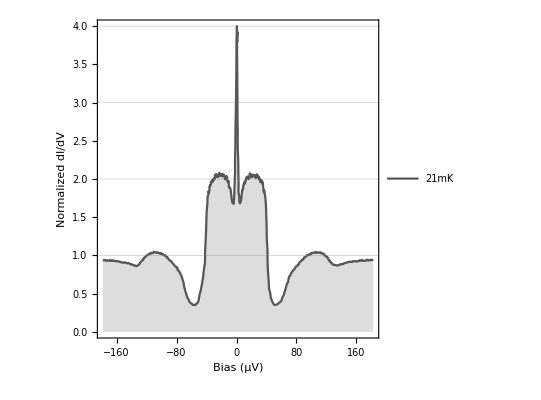

C:\Users\rafae\Documents\ZBCP poster\fig\T_dependence\..\exp.pdf

```mathematica
s={15,FontFamily->"Times New Roman"};

l1=ListPlot[{Map[#{10^6,4/Max[a]}&,a]},Joined->True,Frame->True,
Filling->Axis,
PlotStyle->ColorData[6,"ColorList"],
PlotLegends->Placed[{"21mK","350mK"},{Scaled[{0.8,0.8}],{0.5,0.5}}],
LabelStyle->Directive[15],
Axes->False,
FrameLabel->{Style["Bias (μV)",s],Style["Normalized dI/dV",s]},
GridLines->{{},{1,2,3,4}},
AspectRatio->1,
FrameTicksStyle->Directive[s],
FrameStyle->Thickness[0.002]]
Export[NotebookDirectory[]<>"..\exp.pdf",l1]
```

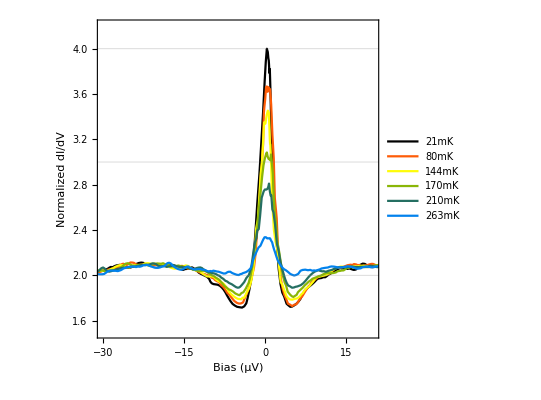

C:\Users\rafae\Documents\ZBCP poster\fig\T_dependence\..\peak.pdf

```mathematica
temp={"21","80","144","170","210","263"};
data={};
Do[
load=Sort@Import[NotebookDirectory[]<>"dIdV"<>temp[[i]]<>"mK.DAT","Table",HeaderLines->1];
load=MovingAverage[load,4];
If[i==1,mm=Max[load];,];
load=Map[#{10^6,4/mm}&,load];
AppendTo[data,load]
,{i,Length@temp}]
l2=ListPlot[data,
Joined->True,Frame->True,
Filling->False,
PlotStyle->ColorData[3,"ColorList"],
PlotLegends->Placed[Map[#<>"mK"&,temp],{Scaled[{0.83,0.7}],{0.5,0.5}}],
LabelStyle->Directive[15],
Axes->False,
FrameLabel->{Style["Bias (μV)",s],Style["Normalized dI/dV",s]},
GridLines->{{},{1,2,3,4}},
AspectRatio->1,
FrameTicksStyle->Directive[s],
FrameStyle->Thickness[0.002],
PlotRange->{{-30,20},{1.5,4.2}}]
Export[NotebookDirectory[]<>"..\peak.pdf",l2]
```

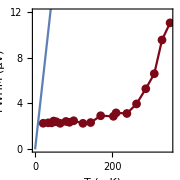

C:\Users\rafae\Documents\ZBCP poster\fig\T_dependence\..\inset.pdf

```mathematica
temp={"21","34","43","48","55","65","80","89","100","124","144","170","203","210","238","263","287","309","329","350"};
data={};
Do[
load=Sort@Import[NotebookDirectory[]<>"dIdV"<>temp[[i]]<>"mK.DAT","Table",HeaderLines->1];
load=MovingAverage[load,4];
If[i==1,mm=Max[load];,];
load=Map[#{10^6,4/mm}&,load];
AppendTo[data,load]
,{i,Length@temp}]
g=amp*Exp[-(x-x0)^2/(2 σ^2)]+2;
fwhm={};
bdy=7;
Do[
d=Select[data[[i]],bdy>#[[1]]>-bdy&];
fit=FindFit[d,g,{σ,amp,x0},x];
AppendTo[fwhm,2 √(2 Log[2])σ/.fit];
,{i,Length@temp}]
(*Show[ListPlot@d,Plot[g/.fit,{x,-bdy,bdy}]]*)
l3=Show[
ListPlot[Transpose@{ToExpression@temp,fwhm},
Joined->True,PlotMarkers->Automatic, Frame->True,
Filling->False,
PlotStyle->ColorData[6,"ColorList"],
LabelStyle->Directive[15],
Axes->False,
FrameLabel->{Style["T (mK)",s],Style["FWHM (μV)",s]},
AspectRatio->1,
FrameTicksStyle->Directive[s],
FrameStyle->Thickness[0.002],PlotRange->{0,12},
ImageSize->Small,
FrameTicks->{{{0,4,8,12},None},{{0,100,200,300},None}}],
Plot[3.5 8.617333262145*10^-2 t,{t,0,300}]
]
Export[NotebookDirectory[]<>"..\inset.pdf",l3]
```